# Muon Beam Dump: BSM Scalar with FeynCalc

#### Notebook Description:

In this notebook, we go through calculations of cross sections for the production of beyond the Standard Model (BSM) states in a muon beam dump experiment, through scattering of the form
μ^-N → μ^- N ϕ_BSM
where ϕ_BSM indicates a BSM scalar.

We set up the relevant definitions and typesetting in Setup and perform tests in Tests.

Details:

In Tests, we:
* Compare certain results against analytic calculations;
* Compare our results against those of 1609.06781 and find agreement up to terms which are suppressed by factors of O(q^2).

# Setup

Setting up directories

```mathematica
$DirectorySetup="/Users/sam/Documents/Research/BeamDumpBSM/setup/directories.m";
Get[$DirectorySetup]
```

### FeynCalc, Models, Typesetting

#### Loading FeynCalc and FeynArts

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

#### Initializing and Typesetting Model

Model Independent

```mathematica
MakeBoxes[epsel,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), e]\)";
MakeBoxes[epsmu,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(μ\)]\)";
```

Model Specific

```mathematica
InitializeModel["scalar_mubeamdump"];
```

loading generic model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/scalar_mubeamdump.mod

> 6 particles (incl. antiparticles) in 4 classes

> $CounterTerms are ON

> 4 vertices

classes model {scalar_mubeamdump} initialized

Names, couplings, etc.

```mathematica
MakeBoxes[phi,TraditionalForm]:="\!\(\(ϕ\)\)";

MakeBoxes[mBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(ϕ\)]\)";

MakeBoxes[gel,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), e]\)";
MakeBoxes[gmu,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), \(μ\)]\)";
```

Kinematic Properties of the BSM final state:

```mathematica
MakeBoxes[EBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(ϕ\)]\)";
MakeBoxes[betaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(β\), \(ϕ\)]\)";
MakeBoxes[thetaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(θ\), \(ϕ\)]\)";
```

#### Other Typesetting

Outgoing lepton:

```mathematica
MakeBoxes[pprime,TraditionalForm]:="\!\(\*p'\)";
```

Beam and Target:

```mathematica
MakeBoxes[E0,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(0\)]\)";
MakeBoxes[mTar,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(T\)]\)";
```

SM Parameters:

```mathematica
MakeBoxes[mu,TraditionalForm]:="\!\(\*SubscriptBox[\(μ\)]\)";

MakeBoxes[mel,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), e]\)";
MakeBoxes[mmu,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(μ\)]\)";

MakeBoxes[alphaEM,TraditionalForm]:="\!\(\*SubscriptBox[\(α\), EM]\)";
```

#### Replacement Rules

```mathematica
BeamDumpCouplingRules = {gel->epsel e,gmu->epsmu e,e^2->4π alphaEM};
```

### 2→2 Kinematics

#### Typesetting

We denote the Mandelstam invariants for the effective 2 -> 2 process that emerges due to Weiszäcker-Williams (WW) with a subscript 2 :

```mathematica
MakeBoxes[s2,TraditionalForm]:="\!\(\*SubscriptBox[\(s\), \(2\)]\)";
MakeBoxes[t2,TraditionalForm]:="\!\(\*SubscriptBox[\(t\), \(2\)]\)";
MakeBoxes[u2,TraditionalForm]:="\!\(\*SubscriptBox[\(u\), \(2\)]\)";
```

They have counterparts with a tilde:

```mathematica
MakeBoxes[stilde,TraditionalForm]:="\!\(\*OverscriptBox[\(s\), \(~\)]\)";
MakeBoxes[ttilde,TraditionalForm]:="\!\(\*OverscriptBox[\(t\), \(~\)]\)";
MakeBoxes[utilde,TraditionalForm]:="\!\(\*OverscriptBox[\(u\), \(~\)]\)";
```

Furthermore, there are beam-related kinematic variables of interest:

#### Mandelstam and Kinematic Variable Setup

t (with no subscript) denotes the “momentum transfer” mediated by the intermediate WW photon:

```mathematica
t=-SP[q,q];
```

Mandelstam Setup with awesome built-in FeynCalc functions

```mathematica
SetMandelstam[s2, t2, u2,
p (* Incoming Lepton *),
q (* "Incoming" off-shell photon*),
-1*pprime (* Outgoing Lepton *),
-1*k (* Outgoing BSM Final State *),
 mmu (*Lepton*), q (*photon*), mmu (*Lepton*), mBSM (*BSM*)];
```

Replacements Involving 2 -> 2 Mandelstams :

```mathematica
TwoToTildeEl = {s2->stilde+mel^2,u2->utilde+mel^2};
TwoToTildeMu = {s2->stilde+mmu^2,u2->utilde+mmu^2};
```

```mathematica
TildeToTwoEl = {stilde->s2-mel^2,utilde->u2-mel^2};
TildeToTwoMu = {stilde->s2-mmu^2,utilde->u2-mmu^2};
```

#### Tests

Basics

```mathematica
SP[p,p]
SP[pprime,pprime]
SP[q,q]
SP[k,k]
```

m_μ^2

m_μ^2

q^2

m_ϕ^2

Mandelstams

```mathematica
(* Subscript[s, 2] and s tilde*)
SP[pprime,pprime] + 2SP[pprime,k] + SP[k,k]//FullSimplify
SP[pprime,pprime] + 2SP[pprime,k] + SP[k,k]-mmu^2/.TwoToTildeMu//FullSimplify
```

s_2

s̃

```mathematica
(* Subscript[u, 2] and u tilde*)
SP[p,p] - 2SP[p,k] + SP[k,k]//FullSimplify
SP[p,p] - 2SP[p,k] + SP[k,k]-mmu^2/.TwoToTildeMu//FullSimplify
```

u_2

ũ

```mathematica
(* Subscript[t, 2] *)
SP[pprime,pprime] - 2SP[pprime,p] + SP[p,p]//FullSimplify
```

t_2

#### “Limit Checker” Replacement Rules:

```mathematica
AllMassless = {mel->0,mmu->0,mBSM ->0,
(* also, zero virtuality for the WW photon: *)
SP[q,q]->0,SP[q,q]^2->0};
```

```mathematica
mmu//.AllMassless
```

0

### Loading Function Definitions

```mathematica
Get[$scalar2to2Functions]
```

```mathematica
keys = {"Squared, Spin-Averaged Matrix Element",
"Squared, Spin-Averaged Matrix Element on-shell",
"dσ/(d (p . k))", "dσ/(d (p . k)) on-shell",
"dσ/(d (p . k)) near tmin", "dσ/(d (p . k)) on-shell near tmin",
"A^(2 → 2)", "A^(2 → 2) on-shell",
"A^(2 → 2) near tmin", "A^(2 → 2) on-shell near tmin"};
```

```mathematica
Do[var[keys[[i]]]=scalar2to2[keys[[i]]],{i,Length[keys]}]
```

```mathematica
amplitudeSquared=var["Squared, Spin-Averaged Matrix Element"]
```

-((e^2 y_μ^2 (-m_ϕ^2 (2 m_μ^4 (q^2-5 (s_2+u_2))-2 m_μ^2 (q^2 (s_2+u_2)-2 s_2 u_2)+q^2 (s_2^2+u_2^2)+12 m_μ^6+2 s_2 u_2 (s_2+u_2))+(2 m_μ^2-s_2-u_2) (m_μ^4 (8 q^2-3 (s_2+u_2))+m_μ^2 (-4 q^2 (s_2+u_2)+s_2^2-4 s_2 u_2+u_2^2)+10 m_μ^6-s_2 u_2 (s_2+u_2))+2 m_ϕ^4 (m_μ^2-s_2) (m_μ^2-u_2)))/((m_μ^2-s_2)^2 (m_μ^2-u_2)^2))

# Tests

## Squared Amplitude :

### Getting Contributions from Specific Channels

#### Diagrams

```mathematica
(* Use output from this cell to get the s- and u-channel diagrams*)
diagrams2to2;
```

```mathematica
sDiagram = TopologyList(Process->{F(2),V(1)}->{F(2),S(1)},Model->{"scalar_mubeamdump"},GenericModel->{"Lorentz"},InsertionLevel->{Classes},ExcludeParticles->{},ExcludeFieldPoints->{},LastSelections->{})(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(5),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(6),Field(4)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6),Field(5)))->Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)->F(2),Field(2)->V(1),Field(3)->-F(2),Field(4)->S(1),Field(5)->F)->Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)->F(2),Field(2)->V(1),Field(3)->-F(2),Field(4)->S(1),Field(5)->F(2)))));
```

```mathematica
uDiagram = TopologyList(Process->{F(2),V(1)}->{F(2),S(1)},Model->{"scalar_mubeamdump"},GenericModel->{"Lorentz"},InsertionLevel->{Classes},ExcludeParticles->{},ExcludeFieldPoints->{},LastSelections->{})(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(6),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(5),Field(4)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6),Field(5)))->Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)->F(2),Field(2)->V(1),Field(3)->-F(2),Field(4)->S(1),Field(5)->F)->Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)->F(2),Field(2)->V(1),Field(3)->-F(2),Field(4)->S(1),Field(5)->F(2)))));
```

#### Drawing Diagrams

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

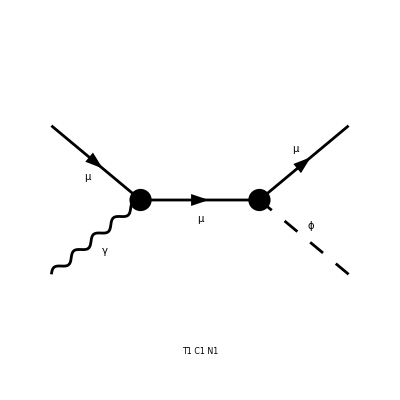

```mathematica
Paint[sDiagram];
```

> Top. 1 aebf/cfde/ef.m, 0 diagrams

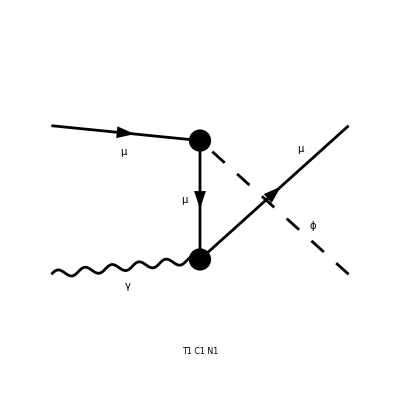

```mathematica
Paint[uDiagram];
```

#### (“Squared”) Amplitudes

```mathematica
sAmplitude=FCFAConvert[CreateFeynAmp[sDiagram], IncomingMomenta->{p,q},
	OutgoingMomenta->{pprime,k},UndoChiralSplittings->True,ChangeDimension->4,
	TransversePolarizationVectors->{q}, List->False, SMP->True,
	Contract->True];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

```mathematica
uAmplitude=FCFAConvert[CreateFeynAmp[uDiagram], IncomingMomenta->{p,q},
	OutgoingMomenta->{pprime,k},UndoChiralSplittings->True,ChangeDimension->4,
	TransversePolarizationVectors->{q,k}, List->False, SMP->True,
	Contract->True];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

```mathematica
sAmplitudeSquared=(sAmplitude (ComplexConjugate[sAmplitude]))//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//
FullSimplify;
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

```mathematica
uAmplitudeSquared=(uAmplitude (ComplexConjugate[uAmplitude]))//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//
FullSimplify;
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

```mathematica
suAmplitudeSquared=(
sAmplitude (ComplexConjugate[uAmplitude])
)//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//
FullSimplify;
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

```mathematica
usAmplitudeSquared=(
uAmplitude (ComplexConjugate[sAmplitude])
)//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//
FullSimplify;
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

#### Explicit Expressions

```mathematica
Numerator[sAmplitudeSquared/(gmu^2 e^2)]//.TwoToTildeMu//Expand
```

-s̃ ũ-4 s̃ m_μ^2-4 q^2 m_μ^2+q^2 m_ϕ^2-8 m_μ^4+2 m_μ^2 m_ϕ^2

```mathematica
Numerator[uAmplitudeSquared/(gmu^2 e^2)]//.TwoToTildeMu//Expand
```

-s̃ ũ-4 ũ m_μ^2-4 q^2 m_μ^2+q^2 m_ϕ^2-8 m_μ^4+2 m_μ^2 m_ϕ^2

### Comparison to 1609.06781

#### Setting up squared amplitude:

```mathematica
var["Squared, Spin-Averaged Matrix Element from 1609.06781"]=gmu^2 e^2(-(stilde+utilde)^2/(stilde utilde)+2(mBSM^2-4 mmu^2)(((stilde+utilde)/(stilde utilde))^2 mmu^2-t2/(stilde utilde)))//.TildeToTwoMu//TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&;
```

```mathematica
var["Squared, Spin-Averaged Matrix Element from 1609.06781"]=
var["Squared, Spin-Averaged Matrix Element from 1609.06781"]//.TwoToTildeMu//FullSimplify;
```

#### Checking massless behavior:

```mathematica
var["Squared, Spin-Averaged Matrix Element from 1609.06781"]//.AllMassless
```

-(e^2 y_μ^2 (s̃+ũ)^2)/(s̃ ũ)

```mathematica
(amplitudeSquared//.TwoToTildeMu)//.AllMassless//FullSimplify
```

-(e^2 y_μ^2 (s̃+ũ)^2)/(s̃ ũ)

#### Checking massive behavior:

```mathematica
(var["Squared, Spin-Averaged Matrix Element from 1609.06781"]-(amplitudeSquared//.TwoToTildeMu))//FullSimplify
```

-(e^2 q^2 y_μ^2 (m_ϕ^2 (s̃+ũ)^2-4 m_μ^2 ((s̃)^2+4 s̃ ũ+(ũ)^2)))/((s̃)^2 (ũ)^2)

```mathematica
(var["Squared, Spin-Averaged Matrix Element from 1609.06781"]-(amplitudeSquared//.TwoToTildeMu))/.SP[q,q]->0/.(SP[q,q])^2->0//FullSimplify
```

0

```mathematica
(var["Squared, Spin-Averaged Matrix Element from 1609.06781"]-(var["Squared, Spin-Averaged Matrix Element on-shell"]//.TwoToTildeMu))/.SP[q,q]->0/.(SP[q,q])^2->0//FullSimplify
```

0

## A^(2→2):

### Comparison to 1609.06781

#### Setting up A^(2→2):

```mathematica
var["A^(2 → 2) near tmin from 1609.06781"] = x^2/(1-x)+2 (mBSM^2-4 mmu^2)1/utilde^2(utilde x + mBSM^2(1-x) + mmu^2 x^2)//.tMinApproximations;
```

#### Checking massless behavior:

Massless piece of our calculation (clearly agrees):

```mathematica
var["A^(2 → 2) near tmin"]//.AllMassless//FullSimplify
```

-x^2/(x-1)

```mathematica
(var["A^(2 → 2) near tmin from 1609.06781"] - var["A^(2 → 2) near tmin"])//.AllMassless //FullSimplify
```

0

```mathematica
(var["A^(2 → 2) near tmin from 1705.01633"] - var["A^(2 → 2) on-shell near tmin"])//.AllMassless //FullSimplify
```

var(A^(2 → 2) near tmin from 1705.01633)+x+1/(x-1)+1

#### Checking massive behavior (* disagrees because of the O(q^2) terms *):

```mathematica
(var["Squared, Spin-Averaged Matrix Element from 1609.06781"]-(amplitudeSquared//.TwoToTildeMu))//FullSimplify
```

-(e^2 q^2 y_μ^2 (m_ϕ^2 (s̃+ũ)^2-4 m_μ^2 ((s̃)^2+4 s̃ ũ+(ũ)^2)))/((s̃)^2 (ũ)^2)

Preparation:

This seems to be similar to the disagreement we see in later parts of the calculation

```mathematica
(var["Squared, Spin-Averaged Matrix Element from 1609.06781"]-(amplitudeSquared//.TwoToTildeMu))//.tMinApproximations//FullSimplify
```

(e^2 y_μ^2 (m_ϕ^2 x^2-4 m_μ^2 (x (x+2)-2)))/(4 E_0^2 (x-1)^2)

```mathematica
(var["Squared, Spin-Averaged Matrix Element from 1609.06781"]-(var["Squared, Spin-Averaged Matrix Element on-shell"]//.TwoToTildeMu))/.SP[q,q]->0/.(SP[q,q])^2->0//FullSimplify
```

0

```mathematica
Quit[]
```